# Clase 2 Diplomado en Programación Básica

Luis Gerardo Ramirez Archundia

## Listas

```mathematica
a={21,63,8,9};
a[[4]]
b=Range[19]
BarChart[Join[a,b]]
Count[a,1]
ListPlot[Range[12]]
PieChart3D[Range[10,50]]
```

## Ejercicios

1. Use Range para crear la lista {1,2,3,4}

```mathematica
Range[4]
```

{1,2,3,4}

2. Construya la lista de números hasta el 100

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

3. Use Range y Reverse para crear {4,3,2,1}

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

4. Construya la lista de los números del 1 al 50 en orden inverso

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

5. Use Range, Reverse y Join para crear {1,2,3,4,4,3,2,1}

```mathematica
Join[Range[4],Reverse[Range[4]]]
```

{1,2,3,4,4,3,2,1}

6. Use Range y RandomInteger para crear una lista de longitud aleatoria hasta 10

```mathematica
Range[RandomInteger[10]]
```

{1,2,3,4,5,6}

7. Encuentre una forma más simple para Reverse[Reverse[Range[10]]]

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

8. Encuentre una forma más simple para Join[1,2,Join[3,4,5]]

```mathematica
Join[Range[1,2],Range[3,5]]
```

9. Encuentre una forma más simple para Join[Range[10],Join[Range[10],Range[5]]]

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

10. Construya un diagrama de barras con 1,1,2,3,5

```mathematica
BarChart3D[{1,1,2,3,5}]
```

-Graphics3D-

11. Produzca un diagrama circular con los números del 1 al 10

```mathematica
PieChart3D[Range[10]]
```

-Graphics3D-

12. Forme un diagrama de barras de los números consecutivos del 20 al 1

```mathematica
BarChart3D[Reverse[Range[20]]]
```

-Graphics3D-

13. Muestre en una columna los números del 1 al 5.

```mathematica
Column[Range[5]]
```

1
2
3
4
5

14. Presente los cuadrados de 1, 4, 9, 16, 25 sobre una recta numérica.

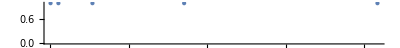

```mathematica
NumberLinePlot[Power[{1,4,9,16,25},2]]
```

15. Forme un gráfico circular con 10 sectores idénticos, cada uno de tamaño 1.

```mathematica
PieChart3D[{Table[1,10]}]
```

-Graphics3D-

16. Presente una columna de los gráficos circulares con 1, 2 y 3 sectores idénticos

```mathematica
Column[{PieChart3D[{1}],PieChart3D[{1,1}],PieChart3D[{1,1,1}]}]
```

-Graphics3D-
-Graphics3D-
-Graphics3D-

17. Forme una lista de gráficos circulares con 1, 2 y 3 sectores idénticos

```mathematica
a={PieChart3D[{1}],PieChart3D[{1,1}],PieChart3D[{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

18. Presente un diagrama de barras con la secuencia 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1.

```mathematica
BarChart3D[Join[Range[10],Reverse[Range[9]]]]
```

-Graphics3D-

19. Cree una lista de los 10 primeros cuadrados en orden inverso

```mathematica
Reverse[Power[Range[10],2]]
```

{100,81,64,49,36,25,16,9,4,1}

20. Calcule el total de los 10 primeros cuadrados

```mathematica
Power[Range[10],2]
Total[Power[Range[10],2]]
```

{1,4,9,16,25,36,49,64,81,100}

385

21. Muestre gráficamente los 10 primeros cuadrados, comenzando por el 1.

```mathematica
PieChart3D[Power[Range[10],2]]
```

-Graphics3D-

22. Cree una lista de los 10 primeros múltiplos de 3.

```mathematica
3*Range[10]
```

{3,6,9,12,15,18,21,24,27,30}

23. Use Sort, Join y Range para crear {1, 1, 2, 2, 3, 3, 4, 4}

```mathematica
Sort[Join[Range[4],Range[4]]]
```

{1,1,2,2,3,3,4,4}

24. Use Range y + para formar la lista de los números del 10 al 20, inclusive.

```mathematica
Range[0,10]+10*{1,1,1,1,1,1,1,1,1,1,1}
```

{10,11,12,13,14,15,16,17,18,19,20}

25. Forme la lista de los 10 primeros cuadrados, usando únicamente Range y Times.

```mathematica
Times[Range[10],Range[10]]
```

{1,4,9,16,25,36,49,64,81,100}

26. Encuentre el número de dígitos en 2^128

```mathematica
Power[2,128]
Length[IntegerDigits[Power[2,128]]]
```

340282366920938463463374607431768211456

39

27. Encuentre el primer dígito de 2^32

```mathematica
Power[2,32]
First[IntegerDigits[Power[2,32]]]
```

4294967296

4

28 . Encuentre los 10 primeros dígitos en 2^100

```mathematica
Power[2,100]
Take[IntegerDigits[Power[2,100]],10]
```

1267650600228229401496703205376

{1,2,6,7,6,5,0,6,0,0}

29. Encuentre el último dígito de 2^37

```mathematica
Power[2,37]
Last[IntegerDigits[Power[2,37]]]
```

137438953472

2

30. Encuentre el penúltimo dígito de 2^32

```mathematica
a=IntegerDigits[Power[2,32]]
Extract[a,Length[a]-1]
```

{4,2,9,4,9,6,7,2,9,6}

9